# Virtual Realizations of Quantum Computers

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

## Quantum Bits

We will be denoting each qubit by the symbol S and accompanying indices .

```mathematica
Let[Qubit,S]
```

The Pauli operators are specified by the last index. For example, the Pauli operator S_j^x is denoted by S[j,1].

```mathematica
S[j,1]
```

S_j^x

```mathematica
S[j,1]**S[j,2]
S[j,1]**S[k,2]
```

ⅈ S_j^z

S_j^x S_k^y

## Dynamical Scheme

### Single-Qubit Gates

Consider a qubit. Let us apply a (fictitious) magnetic field.

```mathematica
Let[Real,B]
opH=Dot[B@{1,2,3},S@{1,2,3}]/2
```

1/2 (B_1 S^x+B_2 S^y+B_3 S^z)

To be specific, we consider the case with the magnetic field between the x-  and z-axis in the xz-plane. The factor of 1/√2is to set the energy (frequency) scale to unit.

```mathematica
B[1]=B[3]=1/Sqrt[2];B[2]=0;
opH
```

1/2 (S^x/(√2)+S^z/(√2))

```mathematica
opU[t_]=MultiplyExp[-I t opH]
opU[t]//Elaborate
```

ⅇ^(-1/2 ⅈ t (S^x/(√2)+S^z/(√2)))

Cos[t/2]-(ⅈ S^x Sin[t/2])/(√2)-(ⅈ S^z Sin[t/2])/(√2)

```mathematica
vec[t_]=opU[t]**Ket[]//Elaborate
```

-(ⅈ 1_S Sin[t/2])/(√2)+␣ (Cos[t/2]-(ⅈ Sin[t/2])/(√2))

This illustrates the Larmor precession (with the qubit regarded as a “spin”).
Technical Note: You need Chop because numerical errors sometimes give 0.+Ket[…], which cannot be handled properly by BlochVector.

```mathematica
vv=BlochVector/@Table[Chop@vec[t],{t,0,8,0.5}];
BlochSphere[{Red,Bead/@vv}]
```

-Graphics3D-

Let us now examine the probabilities for the qubit to be found in the logical basis states.

```mathematica
prob[t_]=Abs[Normal@Matrix@vec[t]]^2
```

{(|Cos[t/2]-(ⅈ Sin[t/2])/(√2)|)^2,1/2 (|Sin[t/2]|)^2}

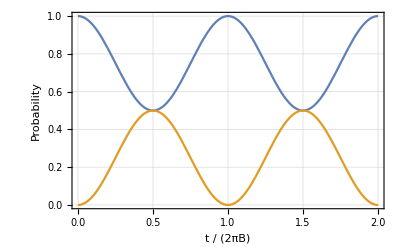

```mathematica
Plot[Evaluate@prob[2 Pi t],{t,0,2},
FrameLabel->{"t / (2πB)","Probability"}]
```

Let us now apply a time-dependent field. It precesses around the z-axis. Note that typically, B_3≫B_1,B_2.

```mathematica
ω=2Pi;
B[1]=Cos[ω t];
B[2]=Sin[ω t];
B[3]=(11/10)ω;
Graphics3D[{Blue,Table[Arrow@Tube@{{0,0,0},B@{1,2,3}},{t,0,1,0.1}]},
PlotRange->ω{{-1,1},{-1,1},{-1,1}}]
```

-Graphics3D-

```mathematica
opH=Dot[B@{1,2,3},S@{1,2,3}]/2
```

1/2 (Cos[2 π t] S^x+(11 π S^z)/5+S^y Sin[2 π t])

```mathematica
opHR=Rotation[-ω t,S[3]]**opH**Rotation[ω t,S[3]]-ω S[3]/2//Elaborate
```

S^x/2+(π S^z)/10

```mathematica
opUR[t_]=MultiplyExp[-I t opHR]
```

ⅇ^(-ⅈ t (S^x/2+(π S^z)/10))

```mathematica
vec[t_]=opUR[t]**Ket[]//Elaborate;
```

This illustrates the precession in the rotating frame, which is called the Rabi oscillation.

```mathematica
vv=BlochVector/@Table[Chop@vec[t],{t,0,8,0.5}];
BlochSphere[{Red,Bead/@vv}]
```

-Graphics3D-

This shows the transition probabilities in the logical basis states. Note that the probabilities are the same both in the lab and rotating frame. The Rabi oscillation frequency is in this particular example is close to one---it is exactly one at resonance.

```mathematica
prob[t_]=Abs[Normal@Matrix@vec[t]]^2;
```

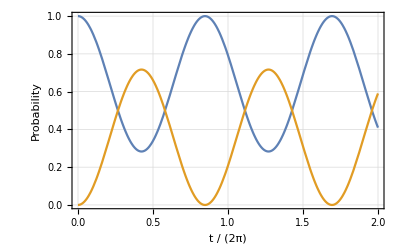

```mathematica
Plot[Evaluate@prob[2 Pi t],{t,0,2},
FrameLabel->{"t / (2π)","Probability"}]
```

### Two-Qubit Gates

## Geometric/Topological Scheme

## Measurement-Based Scheme

Consider an arbitrary state that the first qubit can have.

```mathematica
vec=Ket[]c[0]+Ket[S[1]->1]c[1];
vec//LogicalForm
```

c_0 0_S_1+c_1 1_S_1

This shows the most elementary quantum circuit model that is used for a measurement-based quantum computation.

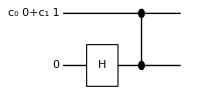

```mathematica
qc=QuissoCircuit[vec,LogicalForm[Ket[],S[2]],S[2,6],CZ[S[1],S[2]],"PortSize"->{2,0.5}]
```

Here is the result of the operations of the gates.

```mathematica
out=Elaborate[qc]
```

(c_0 ␣)/(√2)-(c_1 1_S_11_S_2)/(√2)+(c_1 1_S_1)/(√2)+(c_0 1_S_2)/(√2)

It is useful to rewrite the resulting state in the following form.

```mathematica
new=QuissoFactor[out,S[1]];
new//LogicalForm
```

0_S_1⊗((c_0 0_S_2)/(√2)+(c_0 1_S_2)/(√2))+1_S_1⊗((c_1 0_S_2)/(√2)-(c_1 1_S_2)/(√2))

Using the relation between the CNOT and CZ gate, the following is an equivalent quantum circuit model.

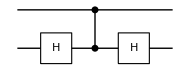
-Graphics-=-Graphics-

```mathematica
Row@{QuissoCircuit[CNOT[S[1],S[2]]],"=",QuissoCircuit[S[2,6],CZ[S[1],S[2]],S[2,6]]}
```

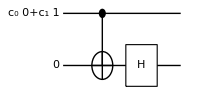

```mathematica
new=QuissoCircuit[vec,LogicalForm[Ket[],S[2]],CNOT[S[1],S[2]],S[2,6],"PortSize"->{2,0.5}]
```

```mathematica
Elaborate[qc]-Elaborate[new]
```

0

Consider a quantum circuit model of the following form.

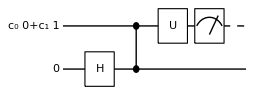

```mathematica
opU=Rotation[ϕ,S[1,1],"Label"->"U"];
qc=QuissoCircuit[vec,LogicalForm[Ket[],S[2]],S[2,6],CZ[S[1],S[2]],opU,Measurement[S[1]],"PortSize"->{2,0.5}]
```

```mathematica
out=Elaborate[qc];
QuissoFactor[out]//LogicalForm
```

Measurement::nonum: Cannot perform a measurement on a nonnumeric state vector. Probability half is assumed.

(c_0 Cos[ϕ/2] 0_S_2+c_0 Cos[ϕ/2] 1_S_2-ⅈ c_1 0_S_2 Sin[ϕ/2]+ⅈ c_1 1_S_2 Sin[ϕ/2])/(√2)

To make the structure of the resulting state, let us examine the state before the measurement. In addition, remove the expected Hadamard gate on the second qubit.

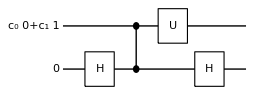

```mathematica
opU=Rotation[ϕ,S[1,1],"Label"->"U"];
qc=QuissoCircuit[vec,LogicalForm[Ket[],S[2]],S[2,6],CZ[S[1],S[2]],opU,S[2,6],"PortSize"->{2,0.5}]
```

```mathematica
out=Elaborate[qc];
QuissoFactor[out,S[1]]//LogicalForm
```

0_S_1⊗(c_0 Cos[ϕ/2] 0_S_2-ⅈ c_1 1_S_2 Sin[ϕ/2])+1_S_1⊗(c_1 Cos[ϕ/2] 1_S_2-ⅈ c_0 0_S_2 Sin[ϕ/2])

## Spin-Boson Model

Denote the qubits by S and the cavity mode by a.

```mathematica
Let[Qubit,S]
Let[Boson,a]
```

This is the Hamiltonian.

```mathematica
opH=Dagger[a]**a+Ω S[3]/2+g(Dagger[a]+a)**S[1]
```

a^†a+g (a S^x+a^†S^x)+(Ω S^z)/2

Here is a truncated basis.

```mathematica
bs=Basis[{a,S}];
LogicalForm@bs
```

{0_a0_S,0_a1_S,1_a0_S,1_a1_S,2_a0_S,2_a1_S,3_a0_S,3_a1_S,4_a0_S,4_a1_S,5_a0_S,5_a1_S}

Here is the matrix representation of the Hamiltonian (showing only part of it), and the eigen-energies for a particular set of parameters.  The matrix representation is not exact as the basis has been truncated.

```mathematica
Ω=1;
g=1/10;
matH=Matrix[opH];
matH[[;;6,;;6]]//MatrixForm
val=N@Eigenvalues[matH]
```

(1/2 | 0 | 0 | 1/10 | 0 | 0
0 | -1/2 | 1/10 | 0 | 0 | 0
0 | 1/10 | 3/2 | 0 | 0 | 1/(5 √2)
1/10 | 0 | 0 | 1/2 | 1/(5 √2) | 0
0 | 0 | 0 | 1/(5 √2) | 5/2 | 0
0 | 0 | 1/(5 √2) | 0 | 0 | 3/2)

{5.52494,4.7328,4.2874,3.69409,3.29609,2.66746,2.32239,1.63601,1.35389,0.594847,-0.505013,0.395102}

Here you can see the (approximate) energy levels of the spin-boson model.

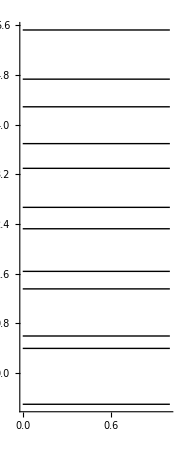

```mathematica
levels=Line@Thread@{Thread@{0,val},Thread@{1,val}};
Graphics[levels,
BaseStyle->Thick,
Axes->{None,True}]
```